#### Sezione e.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[μ_,x_]:= μ x (1-x)
fn[μ_,x_,n_]:= Nest[f[μ,#]&,x,n]
```

```mathematica
(*Manipulate[ListPlot[fn[μ,0.4,#]&/@Range[100]],{μ,0,4}]*)
```

```mathematica
conf[μ_,n_,iterations_]:=Length[Union[Round[10^4(fnC[μ,0.4,iterations+#]-fnC[μ,0.4,iterations]),1]& /@Range[2^n]]]
```

```mathematica
fnC=Compile[{{μ,_Real},{x,_Real},{n,_Integer}},Nest[μ #(1-#)&,x,n]]
```

CompiledFunction[…]

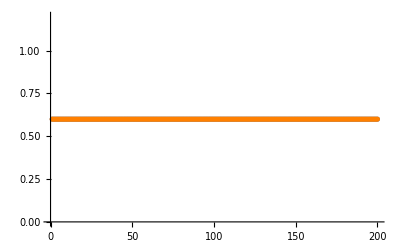

```mathematica
Show[ListPlot[fn[2.5,0.4,#]&/@Range[200]],ListPlot[fn[2.5,0.4001,#]&/@Range[200],PlotStyle->Orange]]
```

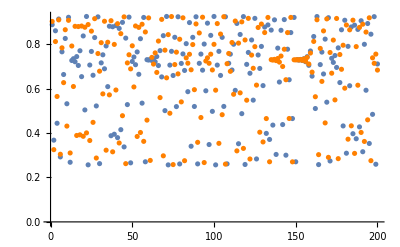

```mathematica
Show[ListPlot[fn[3.7,0.4,#]&/@Range[200]],ListPlot[fn[3.7,0.4+10^14 $MachineEpsilon,#]&/@Range[200],PlotStyle->Orange]]
```

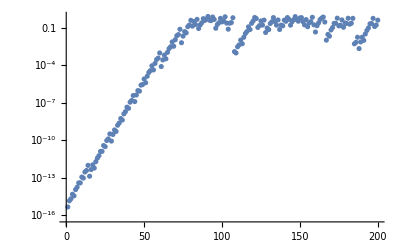

```mathematica
ListLogPlot[Abs[fn[3.8,0.4,#]-fn[3.8,0.4+2 $MachineEpsilon,#]]&/@Range[200]]
```

mmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmmm

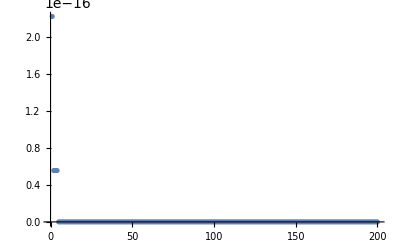

```mathematica
ListPlot[Abs[fn[2,0.4,#]-fn[2,0.4+2 $MachineEpsilon,#]]&/@Range[200]]
```